# Fourier

```mathematica
makeFourierGraph[freqs_,sinCoeffsInit_,cosCoeffsInit_,offsetFixed_]:=Module[
{nFourier,layerDefns,layerConn,graph}
,
nFourier=Length[freqs];

If[nFourier≠0
,

layerDefns=<|
(* Offset *)
"offset"->NetArrayLayer["Output"->1,"Array"->offsetFixed,LearningRateMultipliers->None],

(* Freqs, coeffs *)
"cosCoeff"->NetArrayLayer["Output"->nFourier,"Array"->cosCoeffsInit],
"sinCoeff"->NetArrayLayer["Output"->nFourier,"Array"->sinCoeffsInit],
"freqs"->NetArrayLayer["Output"->nFourier,LearningRateMultipliers->None,"Array"->freqs],

(* Norm *)
"range"->FunctionLayer[Max[1,Total[Abs[#sinCoeff]]+Total[Abs[#cosCoeff]]+10^-8]&],

(* FT *)
"ft"->FunctionLayer[#offset+(Total[#sinCoeff*Sin[(#tpt-1)*#freqs]]+Total[#cosCoeff*Cos[(#tpt-1)*#freqs]])/#range&,"tpt"->1,"freqs"->nFourier,"sinCoeff"->nFourier,"cosCoeff"->nFourier,"offset"->1],
"ftFlatten"->PartLayer[1]
|>;

layerConn={
(* Offset *)
"offset"->NetPort["ft","offset"],

(* Norm *)
"sinCoeff"->NetPort["range","sinCoeff"],
"cosCoeff"->NetPort["range","cosCoeff"],

(* Remaining FT *)
"freqs"->NetPort["ft","freqs"],
"sinCoeff"->NetPort["ft","sinCoeff"],
"cosCoeff"->NetPort["ft","cosCoeff"],
"range"->NetPort["ft","range"],
"ft"->"ftFlatten"
};

,

layerDefns=<|
(* Offset *)
"offset"->NetArrayLayer["Output"->1,"Array"->offsetFixed,LearningRateMultipliers->None],
"ftFlatten"->PartLayer[1]
|>;

layerConn={
(* Offset *)
"offset"->"ftFlatten"
};

];

graph=NetGraph[layerDefns,layerConn];
Return[graph]
]
```

```mathematica
minMax[x_,nFourier_]:=Map[Max[-1.0/nFourier,Min[1.0/nFourier,#]]&,x];
```

## Test

```mathematica
freqsTest={1,2,3,3};
sinCoeffsInitTest={-0.008,0.03,0.02,0.01};
cosCoeffsInitTest={0.001,0.05,0.001,0.005};
offsetFixedTest={1.0};

graph=makeFourierGraph[freqsTest,sinCoeffsInitTest,cosCoeffsInitTest,offsetFixedTest];
```

0.125

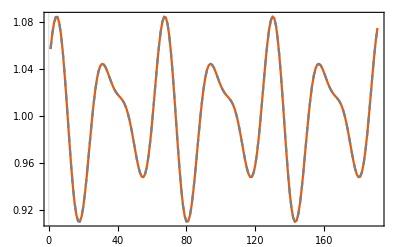

```mathematica
tptsPltTest=Table[tpt,{tpt,1,20,0.1}];

range=Total[Abs[sinCoeffsInitTest]+Abs[cosCoeffsInitTest]]+10^-8
Show[
ListLinePlot[Table[graph[<|"tpt"->{tpt}|>],{tpt,tptsPltTest}]],
ListLinePlot[Table[offsetFixedTest[[1]]+(Sum[sinCoeffsInitTest[[i]]*Sin[freqsTest[[i]]*(tpt-1)]+cosCoeffsInitTest[[i]]*Cos[freqsTest[[i]]*(tpt-1)],{i,Length[freqsTest]}])/Max[range,1],{tpt,tptsPltTest}],PlotStyle->{Gray,Dashed}],
PlotRange->All
]
```

```mathematica
Clear[freqsTest,sinCoeffsInitTest,cosCoeffsInitTest,offsetFixedTest,graph,tptsPltTest,range]
```

# Inverse of diagonal matrix

## Inverse of diagonal matrix

```mathematica
inverseDiagMatLayer[n_]:=Module[
{layerDefns,layerConn}
,
layerDefns=Association[];
If[n>1,
layerDefns["nil"]=NetArrayLayer["Array"->{0.0},LearningRateMultipliers->None];
];
layerDefns["catenate"]=CatenateLayer[];
layerDefns["reshape"]=ReshapeLayer[{n,n}];
Do[
layerDefns["inv"<>ToString[i]]=ElementwiseLayer[#^-1&];
layerDefns["part"<>ToString[i]]=PartLayer[{i,i}];
layerDefns["reshape"<>ToString[i]]=ReshapeLayer[{1}];
,{i,n}];

layerConn={};
Do[
Do[
If[i==j,
AppendTo[layerConn,("part"<>ToString[i])->("inv"<>ToString[i])->("reshape"<>ToString[i])->"catenate"],
AppendTo[layerConn,"nil"->"catenate"]
]
,{j,n}];
,{i,n}];
AppendTo[layerConn,"catenate"->"reshape"];

Return[NetGraph[layerDefns,layerConn,"Input"->{n,n}]]
];
```

## Test

```mathematica
testMat=DiagonalMatrix[{5,6}]//N;
layer=inverseDiagMatLayer[2];

layer[testMat]
Inverse[testMat]
```

{{0.2,0.},{0.,0.166667}}

{{0.2,0.},{0.,0.166667}}

```mathematica
Clear[testMat,layer]
```

# Convert params layer

## Convert b

```mathematica
convertbLayer[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"fn"->FunctionLayer[#b1+Flatten[Transpose[#wt1].#muh1]-Transpose[#wt1].Sqrt[#varh1].Sqrt[#invvarh2].#muh2&,"b1"->nv,"wt1"->{nh,nv},"muh1"->nh,"varh1"->{nh,nh},"muh2"->nh,"invvarh2"->{nh,nh}],
"invvarh2"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh2"]->"invvarh2"->NetPort["fn","invvarh2"]
};
Return[NetGraph[layerDefns,layerConn]];
];
```

## Test

```mathematica
b1Test={1,2,3};
wt1Test={{3,4,5},{6,7,8}};
muh1Test={3,4};
varh1Test={{3,0},{0,2}};
varh2Test={{5,0},{0,6}};
muh2Test={2,8};
b2True=b1Test+Transpose[wt1Test].muh1Test-Transpose[wt1Test].Sqrt[varh1Test].Inverse[Sqrt[varh2Test]].muh2Test//N
b2Actual=convertbLayer[3,2][<|
"b1"->b1Test,
"wt1"->wt1Test,
"muh1"->muh1Test,
"varh1"->varh1Test,
"varh2"->varh2Test,
"muh2"->muh2Test
|>]
```

{1.63961,3.47161,5.30362}

{1.63961,3.47161,5.30362}

```mathematica
Clear[b1Test,wt1Test,muh1Test,varh1Test,varh2Test,muh2Test,b2True,b2Actual]
```

## Convert wt

```mathematica
convertwtLayer[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"fn"->FunctionLayer[Sqrt[#invvarh2].Sqrt[#varh1].#wt1&,"invvarh2"->{nh,nh},"wt1"->{nh,nv},"varh1"->{nh,nh}],
"invvarh2"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh2"]->"invvarh2"->NetPort["fn","invvarh2"]
};
Return[NetGraph[layerDefns,layerConn]];
];
```

## Test

```mathematica
wt1Test={{3,4,5},{6,7,8}};
varh1Test={{3,0},{0,4}};
varh2Test={{5,0},{0,6}};
wt2True=Inverse[Sqrt[varh2Test]].Sqrt[varh1Test].wt1Test//N
wt2Actual=convertwtLayer[3,2][<|
"wt1"->wt1Test,
"varh1"->varh1Test,
"varh2"->varh2Test
|>]
```

{{2.32379,3.09839,3.87298},{4.89898,5.71548,6.53197}}

{{2.32379,3.09839,3.87298},{4.89898,5.71548,6.53197}}

```mathematica
Clear[wt1Test,varh1Test,varh2Test,wt2True,wt2Actual]
```

## Convert b from 0

```mathematica
convertbLayerFrom0[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"fn"->FunctionLayer[#b1-Transpose[#wt1].Sqrt[#invvarh2].#muh2&,"b1"->nv,"wt1"->{nh,nv},"invvarh2"->{nh,nh},"muh2"->nh],
"invvarh2"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh2"]->"invvarh2"->NetPort["fn","invvarh2"]
};
Return[NetGraph[layerDefns,layerConn]];
];
```

## Test

```mathematica
b1Test={1,2,3};
wt1Test={{3,4,5},{6,7,8}};
varh2Test=DiagonalMatrix[{5,6}];
muh2Test={2,8};
b2True=b1Test-Transpose[wt1Test].Sqrt[Inverse[varh2Test]].muh2Test//N
layer=convertbLayerFrom0[3,2];
b2Actual=layer[<|
"b1"->b1Test,
"wt1"->wt1Test,
"varh2"->varh2Test,
"muh2"->muh2Test
|>]
```

{-21.2792,-24.4396,-27.6}

{-21.2792,-24.4396,-27.6}

```mathematica
Clear[b1Test,wt1Test,varh2Test,muh2Test,b2True,layer,b2Actual]
```

## Convert wt from 0

```mathematica
convertwtLayerFrom0[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"fn"->FunctionLayer[Sqrt[#invvarh2].#wt1&,"wt1"->{nh,nv},"invvarh2"->{nh,nh}],
"invvarh2"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh2"]->"invvarh2"->NetPort["fn","invvarh2"]
};
Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
wt1Test={{3,4,5},{6,7,8}};
varh2Test={{5,0},{0,8}};
wt2True=Inverse[Sqrt[varh2Test]].wt1Test//N
wt2Actual=convertwtLayerFrom0[3,2][<|
"wt1"->wt1Test,
"varh2"->varh2Test
|>]
```

{{1.34164,1.78885,2.23607},{2.12132,2.47487,2.82843}}

{{1.34164,1.78885,2.23607},{2.12132,2.47487,2.82843}}

```mathematica
Clear[wt1Test,varh2Test,wt2True,wt2Actual]
```

# Make convert params0 to params layer

## Fourier graph for muh

```mathematica
makeFourierGraphMuh[nh_,freqs_,sinCoeffsInit_,cosCoeffsInit_]:=Module[
{layerDefns,layerConn}
,
layerDefns=Association[];
layerDefns["catenate"]=CatenateLayer[];

Do[
layerDefns["muh"<>ToString[i]]=makeFourierGraph[freqs,sinCoeffsInit,cosCoeffsInit,{0}];
layerDefns["muh"<>ToString[i]<>"Reshape"]=ReshapeLayer[{1}];
,{i,nh}];

layerConn={};

Do[
AppendTo[layerConn,"muh"<>ToString[i]->"muh"<>ToString[i]<>"Reshape"->"catenate"];
,{i,nh}];

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
freqsTest={1,2,3};
sinCoeffsInitTest={1.0,2.0,3.0};
cosCoeffsInitTest={1.0,2.0,3.0};
nhTest=2;
layer=makeFourierGraphMuh[nhTest,freqsTest,sinCoeffsInitTest,cosCoeffsInitTest]
tptTest=4;
layer[tptTest]
```

NetGraph[<>]

{-0.0820332,-0.0820332}

```mathematica
Clear[freqsTest,sinCoeffsInitTest,cosCoeffsInitTest,nhTest,layer,tptTest]
```

## Fourier graph for varh

```mathematica
makeFourierGraphVarh[nh_,freqs_,sinCoeffsInit_,cosCoeffsInit_]:=Module[
{layerDefns,layerConn}
,
layerDefns=Association[];
layerDefns["catenate"]=CatenateLayer[];
If[nh>1,
layerDefns["nil"]=NetArrayLayer[Array->{0.0},LearningRateMultipliers->None];
];
layerDefns["reshape"]=ReshapeLayer[{nh,nh}];

Do[
layerDefns["varhDiag"<>ToString[i]]=makeFourierGraph[freqs,sinCoeffsInit,cosCoeffsInit,{1.01}];
layerDefns["varhDiag"<>ToString[i]<>"Reshape"]=ReshapeLayer[{1}];
,{i,nh}];

layerConn={};

Do[
Do[
If[i==j,
AppendTo[layerConn,"varhDiag"<>ToString[i]->"varhDiag"<>ToString[i]<>"Reshape"->"catenate"],
AppendTo[layerConn,"nil"->"catenate"]
]
,{j,nh}];
,{i,nh}];
AppendTo[layerConn,"catenate"->"reshape"];

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
freqsTest={1,2,3};
sinCoeffsInitTest={1.0,2.0,3.0};
cosCoeffsInitTest={1.0,2.0,3.0};
nhTest=2;
layer=makeFourierGraphVarh[nhTest,freqsTest,sinCoeffsInitTest,cosCoeffsInitTest];
tptTest=3;
layer[tptTest]//MatrixForm
```

(0.98621 | 0.
0. | 0.98621)

```mathematica
Clear[freqsTest,sinCoeffsInitTest,cosCoeffsInitTest,nhTest,layer,tptTest]
```

## Convert params 0 to params

```mathematica
makeConvertParams0ToParamsLayer[nv_,nh_,freqs_,muhCosCoeffsInit_,muhSinCoeffsInit_,varhCosCoeffsInit_,varhSinCoeffsInit_]:=Module[
{layerDefns,layerConn,graph}
,
layerDefns=<|
"layerMuh"->makeFourierGraphMuh[nh,freqs,muhSinCoeffsInit,muhCosCoeffsInit],
"layerVarh"->makeFourierGraphVarh[nh,freqs,varhSinCoeffsInit,varhCosCoeffsInit],

"convertblayer"->convertbLayerFrom0[nv,nh],
"flattenb"->FlattenLayer[],
"convertwtlayer"->convertwtLayerFrom0[nv,nh]
|>;

layerConn={
"layerMuh"->NetPort["convertblayer","muh2"],
"layerVarh"->NetPort["convertblayer","varh2"],
"convertblayer"->"flattenb"->NetPort["b2"],

"layerVarh"->NetPort["convertwtlayer","varh2"],
"convertwtlayer"->NetPort["wt2"],

"layerMuh"->NetPort["muh2"],
"layerVarh"->NetPort["varh2"],
NetPort["sig2"]->NetPort["sig2"]
};

graph=NetGraph[layerDefns,layerConn,"sig2"->1];
Return[graph]
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
freqsTest={0.1,0.2,0.3,0.4};
muhCosCoeffsInitTest=ConstantArray[0,4];
muhSinCoeffsInitTest=ConstantArray[0,4];
varhCosCoeffsInitTest=ConstantArray[0,4];varhSinCoeffsInitTest=ConstantArray[0,4];
```

```mathematica
makeConvertParams0ToParamsLayer[nvTest,nhTest,freqsTest,muhCosCoeffsInitTest,muhSinCoeffsInitTest,varhCosCoeffsInitTest,varhSinCoeffsInitTest];
```

```mathematica
Clear[nvTest,nhTest,freqsTest,muhCosCoeffsInitTest,muhSinCoeffsInitTest,varhCosCoeffsInitTest,varhSinCoeffsInitTest]
```

# Import package for tests

```mathematica
SetDirectory[NotebookDirectory[]]
Get["../../package/funcs_rxns_moms.m"]
```

# Make graph for inputs

```mathematica
makeGraphInputsWOSTD[nv_,nh_,freqs_,muhCosCoeffsInit_,muhSinCoeffsInit_,varhCosCoeffsInit_,varhSinCoeffsInit_]:=Module[
{layerDefns,layerConn,graph,rxnName,idx}
,
layerDefns=<|
"convert0"->makeConvertParams0ToParamsLayer[nv,nh,freqs,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit],
"catenate"->CatenateLayer[],
"flattenWt"->FlattenLayer[],
"flattenVarh"->FlattenLayer[]
|>;

layerConn={
NetPort["wt"]->NetPort["convert0","wt1"],
NetPort["b"]->NetPort["convert0","b1"],
NetPort["convert0","wt2"]->"flattenWt"->"catenate",
NetPort["convert0","varh2"]->"flattenVarh"->"catenate",
NetPort["convert0","muh2"]->"catenate",
NetPort["convert0","b2"]->"catenate",
NetPort["convert0","sig2"]->"catenate"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
momentsTest=<|
"mu"->{3,2,6,8,7},
"var"->{
{9.0,0.2,0.1,0.08,0.07},
{0.2,3.0,0.1,0.08,0.07},
{0.1,0.1,6.0,0.08,0.07},
{0.08,0.08,0.1,8.0,0.0},
{0.07,0.07,0.07,0.0,9.0}
}
|>//N;
PositiveSemidefiniteMatrixQ[momentsTest["var"]]

paramsTest=convertMomentsToParams[momentsTest,nvTest]
momentsTest=convertParamsToMoments[nvTest,paramsTest]
PositiveSemidefiniteMatrixQ[momentsTest["var"]]
```

True

<|sig2→8.99866,muh→{8.,7.},varh→{{8.,0.},{0.,9.}},wt→{{0.01,0.01,0.0125},{0.00777778,0.00777778,0.00777778}},b→{2.86556,1.86556,5.84556}|>

<|muv→{3.,2.,6.},muh→{8.,7.},varv→{{9.,0.00134444,0.00154444},{0.00134444,9.,0.00154444},{0.00154444,0.00154444,9.00045}},varvh→{{0.08,0.08,0.1},{0.07,0.07,0.07}},varh→{{8.,0.},{0.,9.}},mu→{3.,2.,6.,8.,7.},var→{{9.,0.00134444,0.00154444,0.08,0.07},{0.00134444,9.,0.00154444,0.08,0.07},{0.00154444,0.00154444,9.00045,0.1,0.07},{0.08,0.08,0.1,8.,0.},{0.07,0.07,0.07,0.,9.}}|>

True

```mathematica
nvTest=3;
nhTest=2;
freqsTest={1,2,3,4};
muhCosCoeffsInit=ConstantArray[0,4];
muhSinCoeffsInit=ConstantArray[0,4];
varhCosCoeffsInit=ConstantArray[0,4];
varhSinCoeffsInit=ConstantArray[0,4];

makeGraphInputsWOSTD[nvTest,nhTest,freqsTest,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit];
```

```mathematica
Clear[nvTest,nhTest,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit,paramsTest,momentsTest,freqsTest]
```